Изначально запишем функцию как вектор для последующего удобства дифференцирования и нахождения выражения.Функция последовательно находит пересечения касательных в данной точке с осью абсцисс.

```mathematica
f = {5,3,-2,1};
```

```mathematica
dotValue[x_,f_List]:=Total[Table[f⟦i⟧*(x)^(i-1),{i,Length@f}]];
```

```mathematica
dif[f_List]/;Length@f == 1:={0};
dif[f_List]:=Table[f⟦i⟧*(i-1),{i,Length@f}]⟦2;;⟧;
```

```mathematica
solveNewton[f_,x0_]:=Module[{x = x0, d = dif[f], k = 1},
While[Abs[dotValue[x,f]]>10^-8 && k<100,


x = x - dotValue[x,f]/dotValue[x,d];
k++;
Print[N@Abs[dotValue[x,f]]];

];
x
]
```

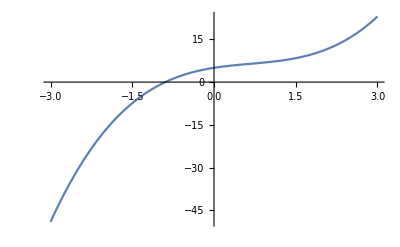

```mathematica
Plot[x^3-2 x^2+3x+5, {x,-3,3}]
```

```mathematica
N@solveNewton[f,1]
```

30.625

7.94128

1.46718

0.0982545

0.000550836

1.76253×10^-8

1.80473×10^-17

-0.894558